```mathematica
SetDirectory[NotebookDirectory[]];
vR1NaCl = Import["./Na_Ca_Cl_potentials/vR1_NaCl.txt", "Table"];
```

```mathematica
fvR1NaCl = Interpolation[vR1NaCl]
```

InterpolatingFunction[{{0.02, 20.}}, <>]

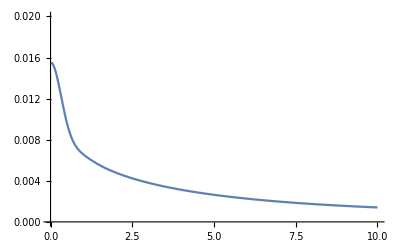

```mathematica
Plot[fvR1NaCl[r], {r, 0.02, 10}, PlotRange->{0,0.02}]
```

```mathematica
vR1CaCl = Import["Na_Ca_Cl_potentials/vR1_CaCl.txt", "Table"];
```

```mathematica
fvR1CaCl = Interpolation[vR1CaCl]
```

InterpolatingFunction[{{0.02, 20.}}, <>]

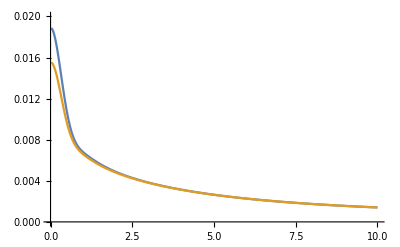

```mathematica
Plot[{fvR1CaCl[r], fvR1NaCl[r]}, {r, 0.02, 10}, PlotRange->{0, 0.02}]
```

```mathematica
s=0.5
```

0.5

```mathematica
ϵ=71
```

71

```mathematica
vuniversal[r_, s1_, s2_]:= Erf[r/s]/r -(1-1/ϵ) (2 Erf[r/Sqrt[s1^2+s^2]]/r - Erf[r/Sqrt[s2^2+s^2]]/r)+(1-1/ϵ)^2(Erf[r/Sqrt[2 s1^2+s^2]]/r - Erf[r/Sqrt[s1^2+s2^2+s^2]]/r)
```

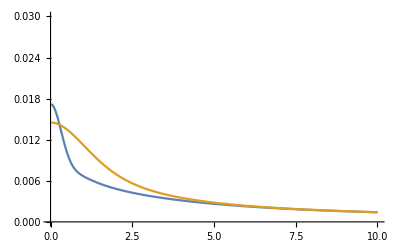

```mathematica
Plot[ {(fvR1CaCl[r]+fvR1NaCl[r])/2,vuniversal[r, 0.01, 1.0]}, {r, 0.02, 10}, PlotRange->{0., 0.03}]
```

```mathematica
v_universal[r, 0, 0.5]
```

v_universal[r,0,0.5]

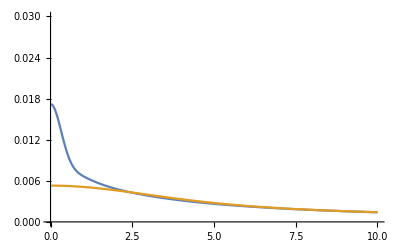

```mathematica
Plot[ {(fvR1CaCl[r]+fvR1NaCl[r])/2,1/ϵ Erf[r/3.0]/r}, {r, 0.02, 10}, PlotRange->{0., 0.03}]
```

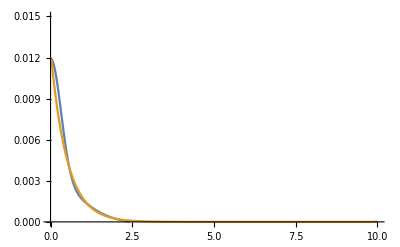

```mathematica
Plot[ {(fvR1CaCl[r]+fvR1NaCl[r])/2-1/ϵ Erf[r/3.0]/r, 0.0125Exp[-2.0r]}, {r, 0.02, 10}, PlotRange->{0., 0.015}]
```

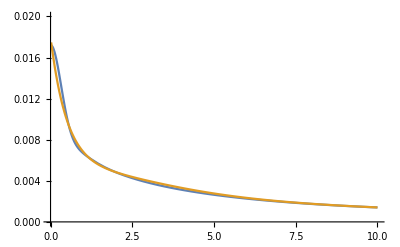

```mathematica
Plot[ {(fvR1CaCl[r]+fvR1NaCl[r])/2,1/ϵ Erf[r/3.0]/r+ 0.9/ϵ Exp[-2.0r]}, {r, 0.02, 10}, PlotRange->{0., 0.02}]
```

```mathematica
N[1/ϵ]
```

0.0140845

```mathematica
0.011/0.014084507042253521
```

0.781

```mathematica
3/(1/0.5)^2
```

0.75

```mathematica
0.75*(1/0.5)^2
```

3.

```mathematica
0.0125*ϵ
```

0.8875

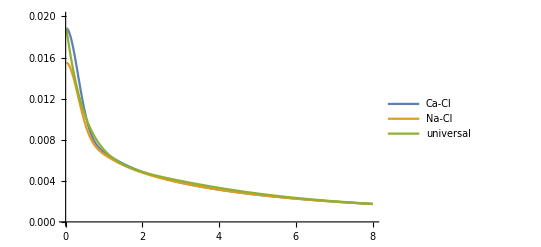

```mathematica
Plot[ {fvR1CaCl[r],fvR1NaCl[r],1/ϵ Erf[r/3.0]/r+ 1.0/ϵ Exp[-2.0r]}, {r, 0.02, 8}, PlotRange->{0., 0.02},PlotLegends->{"Ca-Cl", "Na-Cl","universal"},PlotStyle->{Thick, Thick, Thick}]
```

```mathematica
1.25/0.5
```

2.5

```mathematica
3.0*0.5
```

1.5

```mathematica
1/(0.008*300)
```

0.416667

```mathematica
1/2.5
```

0.4

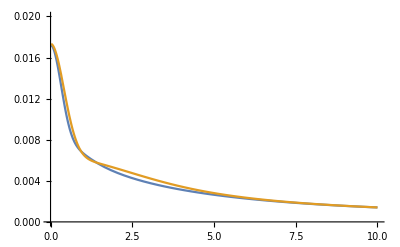

```mathematica
Plot[ {(fvR1CaCl[r]+fvR1NaCl[r])/2, 0.78/ϵ Exp[-0.75(r/s)^2]+1/ϵ Erf[r/(5s)]/r}, 
{r, 0.02, 10}, PlotRange->{0., 0.02}]
```

```mathematica
0.78/71
```

0.0109859

```mathematica
0.75/(0.5)^2
```

3.

```mathematica
-0.75(r/s)^2
```

-3. r^2

```mathematica
1/ϵ Erf[0.001/(2s)]/0.001
```

0.0158927

```mathematica
s
```

0.5